Potential with area and circumference with low power

((a-b-c) (a+b-c) (a-b+c) Rc^2)/(16 (a+b+c)^5 Mc^2)

((a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^4)/(256 (a+b+c)^10 Mc^4)

A0 (1/(15116544 a^4 Mc^4)-1/(3888 a^2 Mc^2))

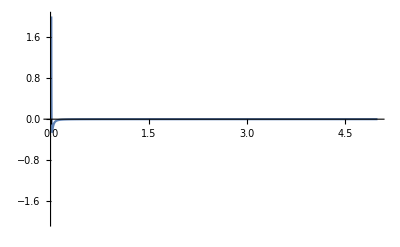

```mathematica
s = (a+b+c)/2;
area2 = Simplify[s*(s-a)*(s-b)*(s-c)]*Mc^4/Rc^4;
long=-area2*(Mc*(a+b+c)/Rc)^-6
short = long^2

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/(18 √6)

4

1

4 E0 ((243 (a-b-c) (a+b-c) (a-b+c) Rc^2)/(2 (a+b+c)^5)+(59049 (a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^4)/(4 (a+b+c)^10))

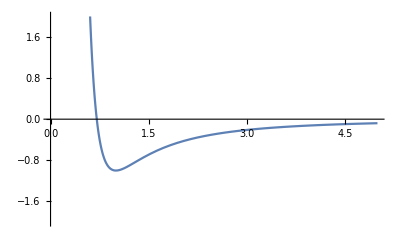

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[2]];
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/(36 √3)

4

√2

4 E0 ((243 (a-b-c) (a+b-c) (a-b+c) Rc^2)/(a+b+c)^5+(59049 (a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^4)/(a+b+c)^10)

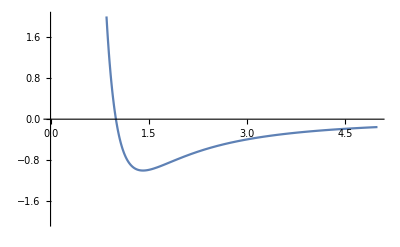

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[2]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

Potential with area and circumference with medium power

((a-b-c) (a+b-c) (a-b+c) Rc^4)/(16 (a+b+c)^7 Mc^4)

((a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^8)/(256 (a+b+c)^14 Mc^8)

A0 (1/(1224440064 a^8 Mc^8)-1/(34992 a^4 Mc^4))

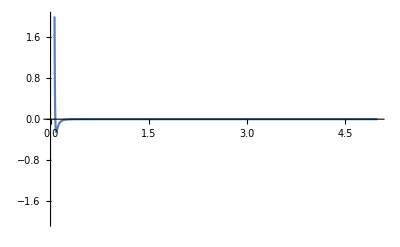

```mathematica
s = (a+b+c)/2;
area2 = Simplify[s*(s-a)*(s-b)*(s-c)]*Mc^4/Rc^4;
long=-area2*(Mc*(a+b+c)/Rc)^-8
short = long^2

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/(3 6^(3/4) Mc)

1/(3 6^(3/4))

4

1

4 E0 ((2187 (a-b-c) (a+b-c) (a-b+c) Rc^4)/(2 (a+b+c)^7)+(4782969 (a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^8)/(4 (a+b+c)^14))

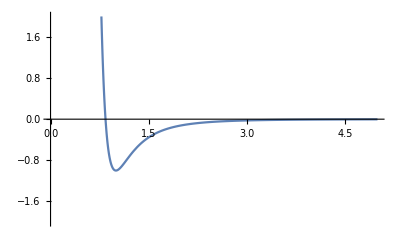

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[4]]
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/(6 3^(3/4))

4

2^(1/4)

4 E0 ((2187 (a-b-c) (a+b-c) (a-b+c) Rc^4)/(a+b+c)^7+(4782969 (a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^8)/(a+b+c)^14)

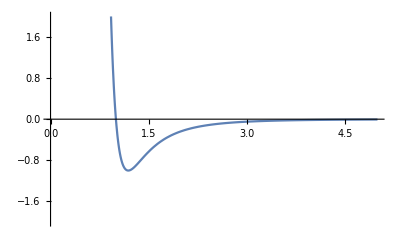

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[4]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

Potential with area and circumference with high power

((a-b-c) (a+b-c) (a-b+c) Rc^6)/(16 (a+b+c)^9 Mc^6)

((a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^12)/(256 (a+b+c)^18 Mc^12)

A0 (1/(99179645184 a^12 Mc^12)-1/(314928 a^6 Mc^6))

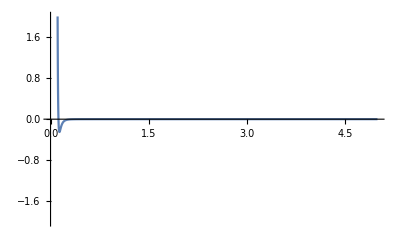

```mathematica
s = (a+b+c)/2;
area2 = Simplify[s*(s-a)*(s-b)*(s-c)]*Mc^4/Rc^4;
long=-area2*(Mc*(a+b+c)/Rc)^-10
short = long^2

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/(3 √6)

4

1

4 E0 ((19683 (a-b-c) (a+b-c) (a-b+c) Rc^6)/(2 (a+b+c)^9)+(387420489 (a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^12)/(4 (a+b+c)^18))

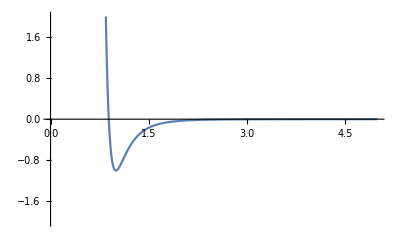

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[2]];
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/(3 2^(2/3) √3)

4

2^(1/6)

4 E0 ((19683 (a-b-c) (a+b-c) (a-b+c) Rc^6)/(a+b+c)^9+(387420489 (a-b-c)^2 (a+b-c)^2 (a-b+c)^2 Rc^12)/(a+b+c)^18)

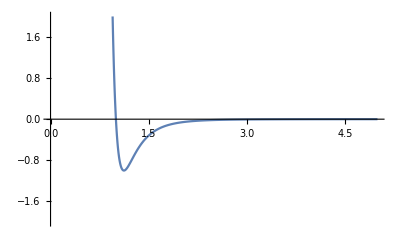

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[2]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

Potential with only circumference high power

-Rc^10/((a+b+c)^10 Mc^10)

Rc^20/((a+b+c)^20 Mc^20)

A0 (1/(3486784401 a^20 Mc^20)-1/(59049 a^10 Mc^10))

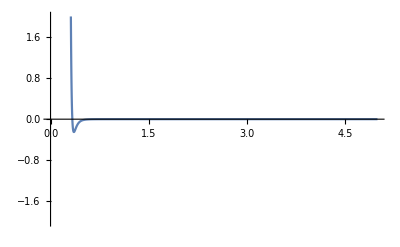

```mathematica
long=-(Mc*(a+b+c)/Rc)^-10
short = long^2

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

2^(1/10)/3

4

1

4 E0 (-(59049 Rc^10)/(2 (a+b+c)^10)+(3486784401 Rc^20)/(4 (a+b+c)^20))

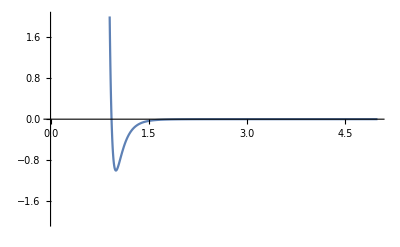

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[2]];
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/3

4

2^(1/10)

4 E0 (-(59049 Rc^10)/(a+b+c)^10+(3486784401 Rc^20)/(a+b+c)^20)

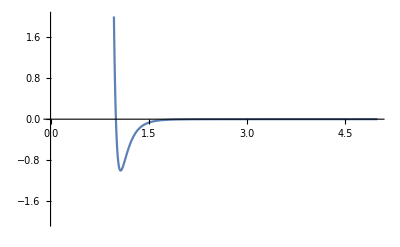

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[2]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

Potential with only circumference medium power

-Rc^8/((a+b+c)^8 Mc^8)

Rc^16/((a+b+c)^16 Mc^16)

A0 (1/(43046721 a^16 Mc^16)-1/(6561 a^8 Mc^8))

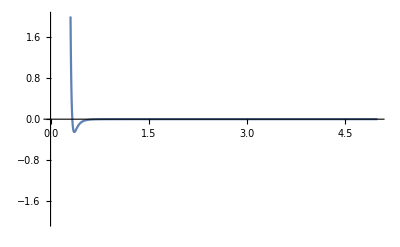

```mathematica
long=-(Mc*(a+b+c)/Rc)^-8
short = long^2

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

2^(1/8)/3

4

1

4 E0 (-(6561 Rc^8)/(2 (a+b+c)^8)+(43046721 Rc^16)/(4 (a+b+c)^16))

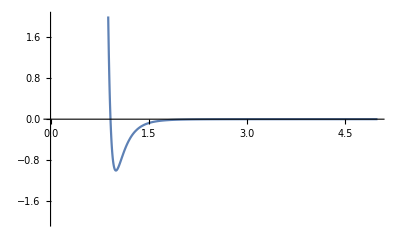

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[4]];
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/3

4

2^(1/8)

4 E0 (-(6561 Rc^8)/(a+b+c)^8+(43046721 Rc^16)/(a+b+c)^16)

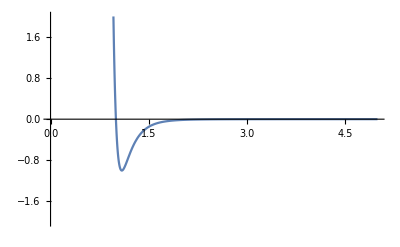

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[4]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

Potential with only circumference low power

-Rc^6/((a+b+c)^6 Mc^6)

Rc^12/((a+b+c)^12 Mc^12)

A0 (1/(531441 a^12 Mc^12)-1/(729 a^6 Mc^6))

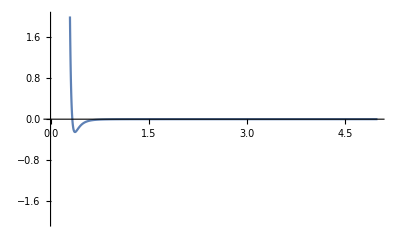

```mathematica
long=-(Mc*(a+b+c)/Rc)^-6
short = long^2

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[2]];
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

2^(1/6)/3

4

1

4 E0 (-(729 Rc^6)/(2 (a+b+c)^6)+(531441 Rc^12)/(4 (a+b+c)^12))

-Graphics-

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[2]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

1/3

4

2^(1/6)

4 E0 (-(729 Rc^6)/(a+b+c)^6+(531441 Rc^12)/(a+b+c)^12)

-Graphics-

Potential with mix of circumference and polynomial terms

Rc^8/(a^8 Mc^8)+Rc^8/(b^8 Mc^8)+Rc^8/(c^8 Mc^8)

-Rc^6/((a+b+c)^6 Mc^6)

A0 (3/(a^8 Mc^8)-1/(729 a^6 Mc^6))

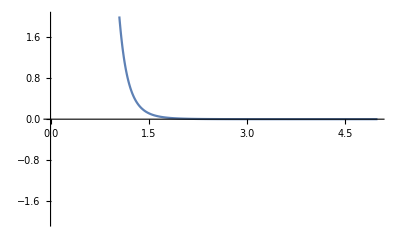

```mathematica
short = (Mc*a/Rc)^-8+(Mc*b/Rc)^-8+(Mc*c/Rc)^-8
long=-(Mc*(a+b+c)/Rc)^-6

totalPotential = A0*E0*(long+short);
totalPotentialtri = totalPotential/.{b->a,c->a, Rc->1, E0->1}
Plot[(totalPotentialtri/.{A0->1, Mc->1})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

54

72301961339136

1

72301961339136 E0 (-Rc^6/(24794911296 (a+b+c)^6)+Rc^8/(72301961339136 a^8)+Rc^8/(72301961339136 b^8)+Rc^8/(72301961339136 c^8))

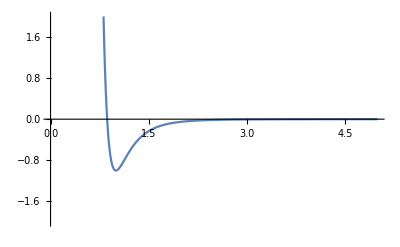

```mathematica
asolmin= (a/.Solve[D[totalPotentialtri,a]==0,a])[[2]];
Mcsolmin=Mc/.Solve[asolmin==1,Mc][[1]]
A0solmin = A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsolmin}

totalPotential/.{A0->A0solmin, Mc->Mcsolmin}
Plot[(totalPotential/.{b->a, c->a,A0->A0solmin, Mc->Mcsolmin})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```

27 √3

72301961339136

2/(√3)

72301961339136 E0 (-Rc^6/(10460353203 (a+b+c)^6)+Rc^8/(22876792454961 a^8)+Rc^8/(22876792454961 b^8)+Rc^8/(22876792454961 c^8))

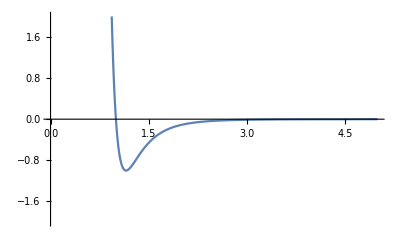

```mathematica
asol= (a/.Solve[totalPotentialtri==0,a])[[2]];
Mcsol=Mc/.Solve[asol==1,Mc][[1]]
A0sol= A0/.Solve[(totalPotentialtri/.{Mc->Mcsolmin, a->1})==-1,A0][[1]]
asolmin/.{Mc->Mcsol}

totalPotential/.{A0->A0sol, Mc->Mcsol}
Plot[(totalPotential/.{b->a, c->a,A0->A0sol, Mc->Mcsol})/.{E0->1, Rc->1}, {a,0,5},PlotRange->{{0, 5}, {-2, 2}}]
```